```mathematica
k[ω_,c_,p_] = Sqrt[ω^2 *(1-I*p^2/(c+I*ω)/ω) ]
```

√((1-(ⅈ p^2)/((c+ⅈ ω) ω)) ω^2)

10

1000

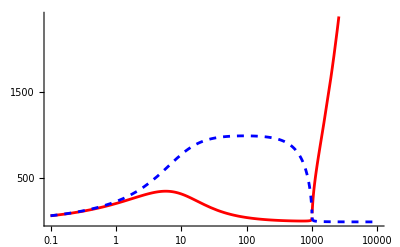

```mathematica
c=10
p=1000
Plot[{Re[k[ω,c,p]],-Im[k[ω,c,p]]},{ω,0.1,10000}, ScalingFunctions-> {"Log","Linear"}, PlotStyle->{{Normal,Red},{Dashed,Blue}},TicksStyle->Directive["Label", 0]]
```